```mathematica
PacletInstall["/home/as/Fourrier/FindBounce-1.1.0.paclet"]
```

PacletInstall::fnotfound: Paclet file /home/as/Fourrier/FindBounce-1.1.0.paclet not found.

$Failed

```mathematica
Needs["FindBounce`"]
```

```mathematica
PacletFind["FindBounce"]
```

{PacletObject[…]}

```mathematica
Names["FindBounce`*"]
```

{BounceFunction,BouncePlot,FindBounce}

```mathematica
?FindBounce
?BounceFunction
?BouncePlot
```

### Test Run

```mathematica
lambda=0.3;
epsilon=0.1;

V[h_,s_]:=((h^2-1)^2)/4+((s^2-1)^2)/4+lambda h^2 s^2-epsilon h;

vars={h,s};

phiTrue={0.89427236,0.72122546};
phiFalse={-0.60590553,0.88302157};

dummyPath=Table[{(1-t)*phiFalse[[1]]+t*phiTrue[[1]]+0.25*Sin[Pi*t],(1-t)*phiFalse[[2]]+t*phiTrue[[2]]-0.15*Sin[Pi*t]},{t,0,1,1/30}];

bf=FindBounce[V[h,s],vars,{phiFalse,phiTrue},"FieldPoints"->dummyPath];

bf["Action"]
```

274.487

### Initial Path Modified

```mathematica
Directory[]
```

/home/as

```mathematica
SetDirectory@NotebookDirectory[]
```

/home/as/Fourier Codes/Fourier+ALGO/FindBounce+Fourier

```mathematica
Get["findbounce_csvK_scan_READY.wl"];
```

Current directory = /home/as/Fourier Codes/Fourier+ALGO/FindBounce+Fourier

Output file will be = /home/as/Fourier Codes/Fourier+ALGO/FindBounce+Fourier/findbounce_csvK_scan_results.csv

Methods = {straight,csvK1,csvK2,csvK3,csvK4,csvK5,csvK6,csvK7,csvK8}

N list = {1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50}

Time limit per FindBounce call = 120 seconds

============================================

Running FindBounce nphi = 1

Vfalse = 0.

Vtrue  = -0.335501

DeltaV = 0.335501

method = straight

status = failed   action = —   time = 0.0209 s

method = csvK1

status = failed   action = —   time = 0.0256 s

method = csvK2

status = failed   action = —   time = 0.0212 s

method = csvK3

status = failed   action = —   time = 0.0210 s

method = csvK4

status = failed   action = —   time = 0.0224 s

method = csvK5

status = failed   action = —   time = 0.0210 s

method = csvK6

status = failed   action = —   time = 0.0224 s

method = csvK7

status = failed   action = —   time = 0.0219 s

method = csvK8

status = failed   action = —   time = 0.0214 s

============================================

Running FindBounce nphi = 2

Vfalse = 0.

Vtrue  = -1.37135

DeltaV = 1.37135

method = straight

status = ok   action = 17.3478   time = 0.3240 s

method = csvK1

status = failed   action = —   time = 0.2852 s

method = csvK2

status = failed   action = —   time = 0.0057 s

method = csvK3

status = failed   action = —   time = 0.0051 s

method = csvK4

status = failed   action = —   time = 0.0058 s

method = csvK5

status = failed   action = —   time = 0.0051 s

method = csvK6

status = failed   action = —   time = 0.0050 s

method = csvK7

status = failed   action = —   time = 0.0060 s

method = csvK8

status = ok   action = 0.388109   time = 0.2209 s

============================================

Running FindBounce nphi = 3

Vfalse = 0.

Vtrue  = -2.46805

DeltaV = 2.46805

method = straight

status = ok   action = 38.7261   time = 0.1169 s

method = csvK1

status = failed   action = —   time = 0.0042 s

method = csvK2

status = failed   action = —   time = 0.0040 s

method = csvK3

status = failed   action = —   time = 0.0041 s

method = csvK4

status = failed   action = —   time = 0.1079 s

method = csvK5

status = ok   action = 18.0508   time = 0.1198 s

method = csvK6

status = ok   action = 20.3216   time = 0.1165 s

method = csvK7

status = ok   action = 20.802   time = 0.1069 s

method = csvK8

status = ok   action = 26.9842   time = 0.1075 s

============================================

Running FindBounce nphi = 4

Vfalse = 0.

Vtrue  = -0.835294

DeltaV = 0.835294

method = straight

status = ok   action = 1284.47   time = 0.0768 s

method = csvK1

status = ok   action = 1075.71   time = 0.0251 s

method = csvK2

status = ok   action = 1176.86   time = 0.0359 s

method = csvK3

status = ok   action = 1210.06   time = 0.0481 s

method = csvK4

status = ok   action = 1225.85   time = 0.0579 s

method = csvK5

status = ok   action = 1245.61   time = 0.0686 s

method = csvK6

status = ok   action = 1300.06   time = 0.0755 s

method = csvK7

status = ok   action = 1308.61   time = 0.0270 s

method = csvK8

status = ok   action = 1298.89   time = 0.0286 s

============================================

Running FindBounce nphi = 5

Vfalse = 0.

Vtrue  = -3.46971

DeltaV = 3.46971

method = straight

status = ok   action = 164.247   time = 0.1383 s

method = csvK1

status = failed   action = —   time = 0.0036 s

method = csvK2

status = ok   action = 0.21887   time = 0.1271 s

method = csvK3

status = ok   action = 87.8885   time = 0.0696 s

method = csvK4

status = ok   action = 35.2907   time = 0.1126 s

method = csvK5

status = ok   action = 55.7611   time = 0.1280 s

method = csvK6

status = ok   action = 112.974   time = 0.1382 s

method = csvK7

status = ok   action = 154.084   time = 0.1508 s

method = csvK8

status = ok   action = 165.575   time = 0.1402 s

============================================

Running FindBounce nphi = 6

Vfalse = 0.

Vtrue  = -3.7323

DeltaV = 3.7323

method = straight

status = ok   action = 310.56   time = 0.1411 s

method = csvK1

status = failed   action = —   time = 0.0057 s

method = csvK2

status = ok   action = 223.702   time = 0.0634 s

method = csvK3

status = ok   action = 278.796   time = 0.0716 s

method = csvK4

status = ok   action = 279.696   time = 0.0981 s

method = csvK5

status = ok   action = 278.476   time = 0.1263 s

method = csvK6

status = ok   action = 294.427   time = 0.1401 s

method = csvK7

status = ok   action = 302.295   time = 0.1567 s

method = csvK8

status = ok   action = 315.026   time = 0.1147 s

============================================

Running FindBounce nphi = 7

Vfalse = 0.

Vtrue  = -0.80376

DeltaV = 0.80376

method = straight

status = ok   action = 24616.4   time = 0.1243 s

method = csvK1

status = ok   action = 24227.8   time = 0.0139 s

method = csvK2

status = ok   action = 24387.6   time = 0.0637 s

method = csvK3

status = ok   action = 23521.3   time = 0.0895 s

method = csvK4

status = ok   action = 24144.4   time = 0.1017 s

method = csvK5

status = ok   action = 24923.9   time = 0.1208 s

method = csvK6

status = ok   action = 25375.2   time = 0.1626 s

method = csvK7

status = ok   action = 25349.7   time = 0.0770 s

method = csvK8

status = ok   action = 24993.7   time = 0.0576 s

============================================

Running FindBounce nphi = 8

Vfalse = 0.

Vtrue  = -3.73111

DeltaV = 3.73111

method = straight

status = ok   action = 1091.88   time = 0.1557 s

method = csvK1

status = ok   action = 832.452   time = 0.0558 s

method = csvK2

status = ok   action = 982.563   time = 0.0579 s

method = csvK3

status = ok   action = 1028.34   time = 0.0940 s

method = csvK4

status = ok   action = 1040.86   time = 0.1199 s

method = csvK5

status = ok   action = 1120.32   time = 0.0419 s

method = csvK6

status = ok   action = 1113.43   time = 0.0451 s

method = csvK7

status = ok   action = 1111.91   time = 0.0505 s

method = csvK8

status = ok   action = 1103.73   time = 0.0536 s

============================================

Running FindBounce nphi = 9

Vfalse = 0.

Vtrue  = -3.66509

DeltaV = 3.66509

method = straight

status = ok   action = 1919.89   time = 0.1772 s

method = csvK1

status = ok   action = 1667.21   time = 0.0654 s

method = csvK2

status = ok   action = 1817.54   time = 0.0752 s

method = csvK3

status = ok   action = 1825.2   time = 0.1050 s

method = csvK4

status = ok   action = 1861.7   time = 0.1460 s

method = csvK5

status = ok   action = 1976.58   time = 0.0801 s

method = csvK6

status = ok   action = 1958.81   time = 0.0540 s

method = csvK7

status = ok   action = 1957.24   time = 0.0570 s

method = csvK8

status = ok   action = 1942.73   time = 0.0628 s

============================================

Running FindBounce nphi = 10

Vfalse = 0.

Vtrue  = -5.60393

DeltaV = 5.60393

method = straight

status = ok   action = 1156.5   time = 0.2199 s

method = csvK1

status = ok   action = 865.354   time = 0.0827 s

method = csvK2

status = ok   action = 1043.01   time = 0.0757 s

method = csvK3

status = ok   action = 1123.56   time = 0.1114 s

method = csvK4

status = ok   action = 1121.94   time = 0.1470 s

method = csvK5

status = ok   action = 1186.61   time = 0.0527 s

method = csvK6

status = ok   action = 1179.5   time = 0.0605 s

method = csvK7

status = ok   action = 1177.93   time = 0.0658 s

method = csvK8

status = ok   action = 1169.25   time = 0.0712 s

============================================

Running FindBounce nphi = 11

Vfalse = 0.

Vtrue  = -7.30705

DeltaV = 7.30705

method = straight

status = ok   action = 937.693   time = 0.2498 s

method = csvK1

status = failed   action = —   time = 0.0758 s

method = csvK2

status = ok   action = 827.441   time = 0.1004 s

method = csvK3

status = ok   action = 903.492   time = 0.1302 s

method = csvK4

status = ok   action = 905.789   time = 0.1722 s

method = csvK5

status = ok   action = 962.275   time = 0.0614 s

method = csvK6

status = ok   action = 955.587   time = 0.0689 s

method = csvK7

status = ok   action = 954.041   time = 0.0778 s

method = csvK8

status = ok   action = 947.186   time = 0.0867 s

============================================

Running FindBounce nphi = 12

Vfalse = 0.

Vtrue  = -4.81274

DeltaV = 4.81274

method = straight

status = ok   action = 3300.97   time = 0.3432 s

method = csvK1

status = ok   action = 3092.96   time = 0.1221 s

method = csvK2

status = ok   action = 3286.76   time = 0.1093 s

method = csvK3

status = ok   action = 3308.86   time = 0.1740 s

method = csvK4

status = ok   action = 3371.79   time = 0.2163 s

method = csvK5

status = ok   action = 3395.59   time = 0.0679 s

method = csvK6

status = ok   action = 3367.72   time = 0.0754 s

method = csvK7

status = ok   action = 3366.74   time = 0.0832 s

method = csvK8

status = ok   action = 3340.75   time = 0.1323 s

============================================

Running FindBounce nphi = 13

Vfalse = 0.

Vtrue  = -7.07821

DeltaV = 7.07821

method = straight

status = ok   action = 1982.94   time = 0.5224 s

method = csvK1

status = ok   action = 1664.02   time = 0.1311 s

method = csvK2

status = ok   action = 1923.09   time = 0.1169 s

method = csvK3

status = ok   action = 2034.37   time = 0.1741 s

method = csvK4

status = ok   action = 2035.56   time = 0.2290 s

method = csvK5

status = ok   action = 2042.2   time = 0.0804 s

method = csvK6

status = ok   action = 2028.99   time = 0.1264 s

method = csvK7

status = ok   action = 2025.59   time = 0.1317 s

method = csvK8

status = ok   action = 2004.93   time = 0.1471 s

============================================

Running FindBounce nphi = 14

Vfalse = 0.

Vtrue  = -7.52703

DeltaV = 7.52703

method = straight

status = ok   action = 2503.84   time = 0.6086 s

method = csvK1

status = ok   action = 2234.21   time = 0.1519 s

method = csvK2

status = ok   action = 2463.17   time = 0.1602 s

method = csvK3

status = ok   action = 2586.04   time = 0.1903 s

method = csvK4

status = ok   action = 2576.02   time = 0.2672 s

method = csvK5

status = ok   action = 2578.74   time = 0.0933 s

method = csvK6

status = ok   action = 2555.67   time = 0.1108 s

method = csvK7

status = ok   action = 2553.77   time = 0.1179 s

method = csvK8

status = ok   action = 2534.1   time = 0.1737 s

============================================

Running FindBounce nphi = 15

Vfalse = 0.

Vtrue  = -4.61349

DeltaV = 4.61349

method = straight

status = ok   action = 11721.9   time = 0.5108 s

method = csvK1

status = ok   action = 11782.   time = 0.0634 s

method = csvK2

status = ok   action = 12058.8   time = 0.1840 s

method = csvK3

status = ok   action = 11682.7   time = 0.2806 s

method = csvK4

status = ok   action = 12167.6   time = 0.3185 s

method = csvK5

status = ok   action = 12117.6   time = 0.1809 s

method = csvK6

status = ok   action = 11947.   time = 0.1140 s

method = csvK7

status = ok   action = 11958.2   time = 0.1264 s

method = csvK8

status = ok   action = 11856.9   time = 0.1459 s

============================================

Running FindBounce nphi = 16

Vfalse = 0.

Vtrue  = -9.00462

DeltaV = 9.00462

method = straight

status = ok   action = 3038.92   time = 0.5597 s

method = csvK1

status = ok   action = 2827.01   time = 0.2025 s

method = csvK2

status = ok   action = 3006.49   time = 0.1693 s

method = csvK3

status = ok   action = 3147.81   time = 0.2620 s

method = csvK4

status = ok   action = 3121.93   time = 0.3536 s

method = csvK5

status = ok   action = 3125.73   time = 0.1144 s

method = csvK6

status = ok   action = 3101.17   time = 0.1386 s

method = csvK7

status = ok   action = 3099.96   time = 0.1412 s

method = csvK8

status = ok   action = 3071.38   time = 0.1646 s

============================================

Running FindBounce nphi = 17

Vfalse = 0.

Vtrue  = -8.61869

DeltaV = 8.61869

method = straight

status = ok   action = 4583.29   time = 0.6126 s

method = csvK1

status = ok   action = 4475.22   time = 0.2250 s

method = csvK2

status = ok   action = 4603.24   time = 0.1964 s

method = csvK3

status = ok   action = 4585.39   time = 0.3295 s

method = csvK4

status = ok   action = 4710.8   time = 0.3850 s

method = csvK5

status = ok   action = 4705.53   time = 0.1438 s

method = csvK6

status = ok   action = 4674.08   time = 0.1591 s

method = csvK7

status = ok   action = 4675.11   time = 0.1681 s

method = csvK8

status = ok   action = 4633.43   time = 0.1868 s

============================================

Running FindBounce nphi = 18

Preprocess failed: FindMinimum failed

============================================

Running FindBounce nphi = 19

Vfalse = 0.

Vtrue  = -3.82474

DeltaV = 3.82474

method = straight

status = ok   action = 60078.4   time = 0.6691 s

method = csvK1

status = ok   action = 60295.   time = 0.0760 s

method = csvK2

status = ok   action = 62888.5   time = 0.2367 s

method = csvK3

status = ok   action = 60203.7   time = 0.3950 s

method = csvK4

status = ok   action = 63225.9   time = 0.5492 s

method = csvK5

status = ok   action = 62908.5   time = 0.6668 s

method = csvK6

status = ok   action = 61793.9   time = 0.2603 s

method = csvK7

status = ok   action = 61098.4   time = 0.2122 s

method = csvK8

status = ok   action = 60662.4   time = 0.2355 s

============================================

Running FindBounce nphi = 20

Vfalse = 0.

Vtrue  = -9.18465

DeltaV = 9.18465

method = straight

status = ok   action = 8285.   time = 0.8394 s

method = csvK1

status = ok   action = 8197.76   time = 0.1388 s

method = csvK2

status = ok   action = 8473.65   time = 0.2740 s

method = csvK3

status = ok   action = 8295.45   time = 0.4600 s

method = csvK4

status = ok   action = 8550.46   time = 0.5416 s

method = csvK5

status = ok   action = 8611.22   time = 0.2666 s

method = csvK6

status = ok   action = 8431.64   time = 0.2115 s

method = csvK7

status = ok   action = 8439.94   time = 0.2382 s

method = csvK8

status = ok   action = 8369.41   time = 0.2610 s

============================================

Running FindBounce nphi = 21

Vfalse = 0.

Vtrue  = -11.122

DeltaV = 11.122

method = straight

status = ok   action = 6279.52   time = 0.9260 s

method = csvK1

status = ok   action = 6185.35   time = 0.2992 s

method = csvK2

status = ok   action = 6392.69   time = 0.3124 s

method = csvK3

status = ok   action = 6321.25   time = 0.5148 s

method = csvK4

status = ok   action = 6531.82   time = 0.5972 s

method = csvK5

status = ok   action = 6506.   time = 0.2961 s

method = csvK6

status = ok   action = 6380.11   time = 0.2429 s

method = csvK7

status = ok   action = 6386.78   time = 0.2591 s

method = csvK8

status = ok   action = 6335.22   time = 0.2817 s

============================================

Running FindBounce nphi = 22

Preprocess failed: FindMinimum failed

============================================

Running FindBounce nphi = 23

Preprocess failed: FindMinimum failed

============================================

Running FindBounce nphi = 24

Preprocess failed: FindMinimum failed

============================================

Running FindBounce nphi = 25

Vfalse = 0.

Vtrue  = -14.3324

DeltaV = 14.3324

method = straight

status = ok   action = 7504.83   time = 1.3988 s

method = csvK1

status = ok   action = 7401.03   time = 0.3469 s

method = csvK2

status = ok   action = 7663.65   time = 0.4583 s

method = csvK3

status = ok   action = 7548.16   time = 0.7910 s

method = csvK4

status = ok   action = 7970.97   time = 0.8103 s

method = csvK5

status = ok   action = 7779.76   time = 0.4370 s

method = csvK6

status = ok   action = 7619.03   time = 0.3482 s

method = csvK7

status = ok   action = 7628.99   time = 0.3902 s

method = csvK8

status = ok   action = 7569.65   time = 0.4380 s

============================================

Running FindBounce nphi = 26

Vfalse = 0.

Vtrue  = -13.4668

DeltaV = 13.4668

method = straight

status = ok   action = 10361.7   time = 1.6049 s

method = csvK1

status = ok   action = 10249.   time = 0.2638 s

method = csvK2

status = ok   action = 10634.   time = 0.5198 s

method = csvK3

status = ok   action = 10384.3   time = 1.0833 s

method = csvK4

status = ok   action = 10745.9   time = 1.0575 s

method = csvK5

status = ok   action = 10761.6   time = 0.4937 s

method = csvK6

status = ok   action = 10513.3   time = 0.4022 s

method = csvK7

status = ok   action = 10529.5   time = 0.4379 s

method = csvK8

status = ok   action = 10451.4   time = 0.4847 s

============================================

Running FindBounce nphi = 27

Vfalse = 0.

Vtrue  = -11.62

DeltaV = 11.62

method = straight

status = ok   action = 18795.9   time = 1.6411 s

method = csvK1

status = ok   action = 18680.2   time = 0.1524 s

method = csvK2

status = ok   action = 19495.8   time = 0.5632 s

method = csvK3

status = ok   action = 18815.4   time = 0.9500 s

method = csvK4

status = ok   action = 19476.4   time = 1.1725 s

method = csvK5

status = ok   action = 19586.7   time = 0.5452 s

method = csvK6

status = ok   action = 19267.8   time = 0.6207 s

method = csvK7

status = ok   action = 19094.9   time = 0.5712 s

method = csvK8

status = ok   action = 18958.1   time = 0.5247 s

============================================

Running FindBounce nphi = 28

Vfalse = 0.

Vtrue  = -16.4698

DeltaV = 16.4698

method = straight

status = ok   action = 9395.58   time = 1.8411 s

method = csvK1

status = ok   action = 9281.77   time = 0.3556 s

method = csvK2

status = ok   action = 9626.72   time = 0.6144 s

method = csvK3

status = ok   action = 9418.67   time = 1.0342 s

method = csvK4

status = ok   action = 10001.2   time = 1.0745 s

method = csvK5

status = ok   action = 9755.54   time = 0.5789 s

method = csvK6

status = ok   action = 9537.79   time = 0.4619 s

method = csvK7

status = ok   action = 9551.32   time = 0.5187 s

method = csvK8

status = ok   action = 9478.87   time = 0.5788 s

============================================

Running FindBounce nphi = 29

Vfalse = 0.

Vtrue  = -14.4175

DeltaV = 14.4175

method = straight

status = ok   action = 15048.6   time = 1.9556 s

method = csvK1

status = ok   action = 15162.4   time = 0.2460 s

method = csvK2

status = ok   action = 15582.3   time = 0.6657 s

method = csvK3

status = ok   action = 15167.2   time = 1.1234 s

method = csvK4

status = ok   action = 16133.1   time = 1.1774 s

method = csvK5

status = ok   action = 15655.   time = 0.6409 s

method = csvK6

status = ok   action = 15404.1   time = 0.7194 s

method = csvK7

status = ok   action = 15277.2   time = 0.5628 s

method = csvK8

status = ok   action = 15168.9   time = 0.6102 s

============================================

Running FindBounce nphi = 30

Vfalse = 0.

Vtrue  = -12.4285

DeltaV = 12.4285

method = straight

status = ok   action = 26249.6   time = 2.1216 s

method = csvK1

status = ok   action = 26051.8   time = 0.1732 s

method = csvK2

status = ok   action = 27340.1   time = 0.7282 s

method = csvK3

status = ok   action = 26221.5   time = 1.2380 s

method = csvK4

status = ok   action = 27143.9   time = 1.4684 s

method = csvK5

status = ok   action = 26854.   time = 0.9208 s

method = csvK6

status = ok   action = 26914.3   time = 0.7884 s

method = csvK7

status = ok   action = 26815.4   time = 0.8589 s

method = csvK8

status = ok   action = 26434.2   time = 0.6677 s

============================================

Running FindBounce nphi = 31

Vfalse = 0.

Vtrue  = -12.3008

DeltaV = 12.3008

method = straight

status = ok   action = 32462.5   time = 2.7169 s

method = csvK1

status = ok   action = 32333.4   time = 0.1922 s

method = csvK2

status = ok   action = 33880.7   time = 0.7139 s

method = csvK3

status = ok   action = 32423.3   time = 1.2370 s

method = csvK4

status = ok   action = 33562.4   time = 1.6053 s

method = csvK5

status = ok   action = 33214.9   time = 0.9749 s

method = csvK6

status = ok   action = 33312.4   time = 0.8420 s

method = csvK7

status = ok   action = 33192.2   time = 0.9310 s

method = csvK8

status = ok   action = 32701.8   time = 0.7271 s

============================================

Running FindBounce nphi = 32

Preprocess failed: FindMinimum failed

============================================

Running FindBounce nphi = 33

Vfalse = 0.

Vtrue  = -9.56226

DeltaV = 9.56226

method = straight

status = ok   action = 88416.5   time = 2.4352 s

method = csvK1

status = ok   action = 88708.   time = 0.2397 s

method = csvK2

status = ok   action = 96516.7   time = 0.7862 s

method = csvK3

status = ok   action = 87995.4   time = 1.5979 s

method = csvK4

status = ok   action = 95557.3   time = 1.6725 s

method = csvK5

status = ok   action = 92585.6   time = 0.8638 s

method = csvK6

status = ok   action = 90942.7   time = 0.9682 s

method = csvK7

status = ok   action = 89704.7   time = 0.7604 s

method = csvK8

status = ok   action = 89140.   time = 0.8340 s

============================================

Running FindBounce nphi = 34

Preprocess failed: FindMinimum failed

============================================

Running FindBounce nphi = 35

Vfalse = 0.

Vtrue  = -5.3158

DeltaV = 5.3158

method = straight

status = ok   action = 660121.   time = 3.1386 s

method = csvK1

status = ok   action = 666139.   time = 0.4415 s

method = csvK2

status = ok   action = 719885.   time = 0.8109 s

method = csvK3

status = ok   action = 727771.   time = 1.5240 s

method = csvK4

status = ok   action = 713244.   time = 1.8779 s

method = csvK5

status = ok   action = 673263.   time = 0.6965 s

method = csvK6

status = ok   action = 670467.   time = 0.7876 s

method = csvK7

status = ok   action = 670758.   time = 0.8751 s

method = csvK8

status = ok   action = 666664.   time = 0.9662 s

============================================

Running FindBounce nphi = 36

Vfalse = 0.

Vtrue  = -15.3579

DeltaV = 15.3579

method = straight

status = ok   action = 42031.4   time = 3.0364 s

method = csvK1

status = ok   action = 42011.2   time = 0.2755 s

method = csvK2

status = ok   action = 45868.5   time = 0.9766 s

method = csvK3

status = ok   action = 42004.5   time = 1.9445 s

method = csvK4

status = ok   action = 45328.6   time = 2.0096 s

method = csvK5

status = ok   action = 43946.6   time = 1.0524 s

method = csvK6

status = ok   action = 42591.5   time = 0.8479 s

method = csvK7

status = ok   action = 42658.7   time = 0.9476 s

method = csvK8

status = ok   action = 42377.4   time = 1.0822 s

============================================

Running FindBounce nphi = 37

Preprocess failed: FindMinimum failed

============================================

Running FindBounce nphi = 38

Vfalse = 0.

Vtrue  = -20.9064

DeltaV = 20.9064

method = straight

status = ok   action = 25444.8   time = 4.1938 s

method = csvK1

status = ok   action = 25320.7   time = 0.3163 s

method = csvK2

status = ok   action = 27728.9   time = 1.0200 s

method = csvK3

status = ok   action = 25431.9   time = 2.1990 s

method = csvK4

status = ok   action = 27352.4   time = 2.3113 s

method = csvK5

status = ok   action = 26563.8   time = 1.2020 s

method = csvK6

status = ok   action = 25793.7   time = 0.9604 s

method = csvK7

status = ok   action = 25836.5   time = 1.0591 s

method = csvK8

status = ok   action = 25659.   time = 1.1699 s

============================================

Running FindBounce nphi = 39

Vfalse = 0.

Vtrue  = -15.7992

DeltaV = 15.7992

method = straight

status = ok   action = 62410.3   time = 3.7931 s

method = csvK1

status = ok   action = 62620.5   time = 0.3479 s

method = csvK2

status = ok   action = 68132.8   time = 1.1772 s

method = csvK3

status = ok   action = 68663.2   time = 2.0654 s

method = csvK4

status = ok   action = 67304.8   time = 2.4157 s

method = csvK5

status = ok   action = 65311.3   time = 1.2782 s

method = csvK6

status = ok   action = 63296.6   time = 1.0262 s

method = csvK7

status = ok   action = 63381.5   time = 1.2018 s

method = csvK8

status = ok   action = 62955.3   time = 1.2505 s

============================================

Running FindBounce nphi = 40

Vfalse = 0.

Vtrue  = -15.5703

DeltaV = 15.5703

method = straight

status = ok   action = 76145.6   time = 4.0210 s

method = csvK1

status = ok   action = 76507.1   time = 0.4228 s

method = csvK2

status = ok   action = 83165.8   time = 1.3330 s

method = csvK3

status = ok   action = 84223.8   time = 2.2617 s

method = csvK4

status = ok   action = 82155.9   time = 2.6861 s

method = csvK5

status = ok   action = 77550.5   time = 1.2093 s

method = csvK6

status = ok   action = 77242.9   time = 1.1704 s

method = csvK7

status = ok   action = 77340.9   time = 1.1672 s

method = csvK8

status = ok   action = 76819.2   time = 1.3508 s

============================================

Running FindBounce nphi = 41

Vfalse = 0.

Vtrue  = -9.57927

DeltaV = 9.57927

method = straight

status = ok   action = 343148.   time = 4.5847 s

method = csvK1

status = ok   action = 345942.   time = 0.4866 s

method = csvK2

status = ok   action = 390786.   time = 1.2666 s

method = csvK3

status = ok   action = 378102.   time = 2.7336 s

method = csvK4

status = ok   action = 370414.   time = 2.3375 s

method = csvK5

status = ok   action = 350169.   time = 1.2586 s

method = csvK6

status = ok   action = 348660.   time = 1.4034 s

method = csvK7

status = ok   action = 348862.   time = 1.5606 s

method = csvK8

status = ok   action = 346613.   time = 1.6943 s

============================================

Running FindBounce nphi = 42

Vfalse = 0.

Vtrue  = -7.08601

DeltaV = 7.08601

method = straight

status = ok   action = 889768.   time = 4.9344 s

method = csvK1

status = ok   action = 901989.   time = 0.5243 s

method = csvK2

status = ok   action = 1.01782×10^6   time = 1.2539 s

method = csvK3

status = ok   action = 983050.   time = 3.0976 s

method = csvK4

status = ok   action = 907661.   time = 1.1806 s

method = csvK5

status = ok   action = 908462.   time = 1.2869 s

method = csvK6

status = ok   action = 904364.   time = 1.3825 s

method = csvK7

status = ok   action = 904935.   time = 1.5366 s

method = csvK8

status = ok   action = 899024.   time = 1.7543 s

============================================

Running FindBounce nphi = 43

Vfalse = 0.

Vtrue  = -25.0458

DeltaV = 25.0458

method = straight

status = ok   action = 30846.6   time = 5.3945 s

method = csvK1

status = ok   action = 30829.2   time = 0.6459 s

method = csvK2

status = ok   action = 33790.7   time = 1.9259 s

method = csvK3

status = ok   action = 31035.4   time = 3.4555 s

method = csvK4

status = ok   action = 33250.   time = 2.7651 s

method = csvK5

status = ok   action = 32211.8   time = 2.0459 s

method = csvK6

status = ok   action = 31254.4   time = 1.5424 s

method = csvK7

status = ok   action = 31311.4   time = 1.7049 s

method = csvK8

status = ok   action = 31093.5   time = 1.8756 s

============================================

Running FindBounce nphi = 44

Vfalse = 0.

Vtrue  = -23.8642

DeltaV = 23.8642

method = straight

status = ok   action = 39052.8   time = 6.0920 s

method = csvK1

status = ok   action = 39084.6   time = 0.5676 s

method = csvK2

status = ok   action = 42750.7   time = 1.7120 s

method = csvK3

status = ok   action = 43200.4   time = 3.2709 s

method = csvK4

status = ok   action = 42140.4   time = 2.7674 s

method = csvK5

status = ok   action = 40811.7   time = 1.9845 s

method = csvK6

status = ok   action = 39570.6   time = 1.6459 s

method = csvK7

status = ok   action = 39638.6   time = 1.8673 s

method = csvK8

status = ok   action = 39369.3   time = 2.0338 s

============================================

Running FindBounce nphi = 45

Vfalse = 0.

Vtrue  = -8.38423

DeltaV = 8.38423

method = straight

status = ok   action = 770569.   time = 6.1302 s

method = csvK1

status = ok   action = 780975.   time = 0.7123 s

method = csvK2

status = ok   action = 882557.   time = 1.6932 s

method = csvK3

status = ok   action = 856537.   time = 3.7160 s

method = csvK4

status = ok   action = 827398.   time = 1.9270 s

method = csvK5

status = ok   action = 785464.   time = 1.6058 s

method = csvK6

status = ok   action = 782264.   time = 1.7679 s

method = csvK7

status = ok   action = 782860.   time = 1.9345 s

method = csvK8

status = ok   action = 778138.   time = 2.1442 s

============================================

Running FindBounce nphi = 46

Vfalse = 0.

Vtrue  = -10.654

DeltaV = 10.654

method = straight

status = ok   action = 451834.   time = 6.3295 s

method = csvK1

status = ok   action = 457228.   time = 0.6675 s

method = csvK2

status = ok   action = 517536.   time = 1.6151 s

method = csvK3

status = ok   action = 503712.   time = 3.8688 s

method = csvK4

status = ok   action = 489815.   time = 3.1415 s

method = csvK5

status = ok   action = 460223.   time = 1.7442 s

method = csvK6

status = ok   action = 458409.   time = 1.9821 s

method = csvK7

status = ok   action = 458815.   time = 2.0408 s

method = csvK8

status = ok   action = 456092.   time = 2.2230 s

============================================

Running FindBounce nphi = 47

Vfalse = 0.

Vtrue  = -4.20425

DeltaV = 4.20425

method = straight

status = ok   action = 7.24066×10^6   time = 7.5616 s

method = csvK1

status = ok   action = 7.37429×10^6   time = 0.6844 s

method = csvK2

status = ok   action = 8.31151×10^6   time = 1.8636 s

method = csvK3

status = ok   action = 8.03568×10^6   time = 4.0517 s

method = csvK4

status = ok   action = 7.38797×10^6   time = 1.5303 s

method = csvK5

status = ok   action = 7.39216×10^6   time = 1.7126 s

method = csvK6

status = ok   action = 7.35991×10^6   time = 1.9438 s

method = csvK7

status = ok   action = 7.36433×10^6   time = 2.0687 s

method = csvK8

status = ok   action = 7.31848×10^6   time = 2.2708 s

============================================

Running FindBounce nphi = 48

Preprocess failed: FindMinimum failed

============================================

Running FindBounce nphi = 49

Vfalse = 0.

Vtrue  = -29.0471

DeltaV = 29.0471

method = straight

status = ok   action = 39610.5   time = 8.1526 s

method = csvK1

status = ok   action = 39643.2   time = 0.7234 s

method = csvK2

status = ok   action = 43677.2   time = 2.5715 s

method = csvK3

status = ok   action = 39915.9   time = 4.8382 s

method = csvK4

status = ok   action = 42852.1   time = 3.5856 s

method = csvK5

status = ok   action = 41361.8   time = 2.7188 s

method = csvK6

status = ok   action = 40023.1   time = 2.0787 s

method = csvK7

status = ok   action = 40115.4   time = 2.3209 s

method = csvK8

status = ok   action = 39861.8   time = 2.6159 s

============================================

Running FindBounce nphi = 50

Vfalse = 0.

Vtrue  = -29.5609

DeltaV = 29.5609

method = straight

status = ok   action = 41878.4   time = 8.5920 s

method = csvK1

status = ok   action = 41922.2   time = 0.8032 s

method = csvK2

status = ok   action = 46121.2   time = 2.5677 s

method = csvK3

status = ok   action = 42171.8   time = 5.3481 s

method = csvK4

status = ok   action = 45309.5   time = 4.1555 s

method = csvK5

status = ok   action = 43744.2   time = 2.8492 s

method = csvK6

status = ok   action = 42330.6   time = 2.2310 s

method = csvK7

status = ok   action = 42423.7   time = 2.4737 s

method = csvK8

status = ok   action = 42154.8   time = 2.7345 s

Saved results to: /home/as/Fourier Codes/Fourier+ALGO/FindBounce+Fourier/findbounce_csvK_scan_results.csv

================ SUMMARY TABLE ================

Saved raw results to: /home/as/Fourier Codes/Fourier+ALGO/FindBounce+Fourier/findbounce_csvK_scan_results.csv

Saved summary to: /home/as/Fourier Codes/Fourier+ALGO/FindBounce+Fourier/findbounce_csvK_scan_summary.csv

DONE. To see CSV files here, run: FileNames["*.csv", Directory[]]

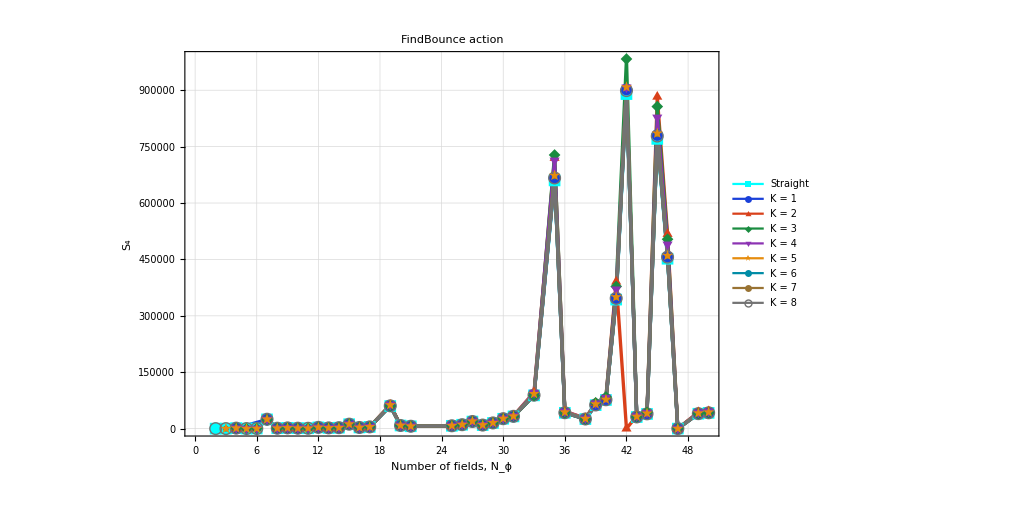

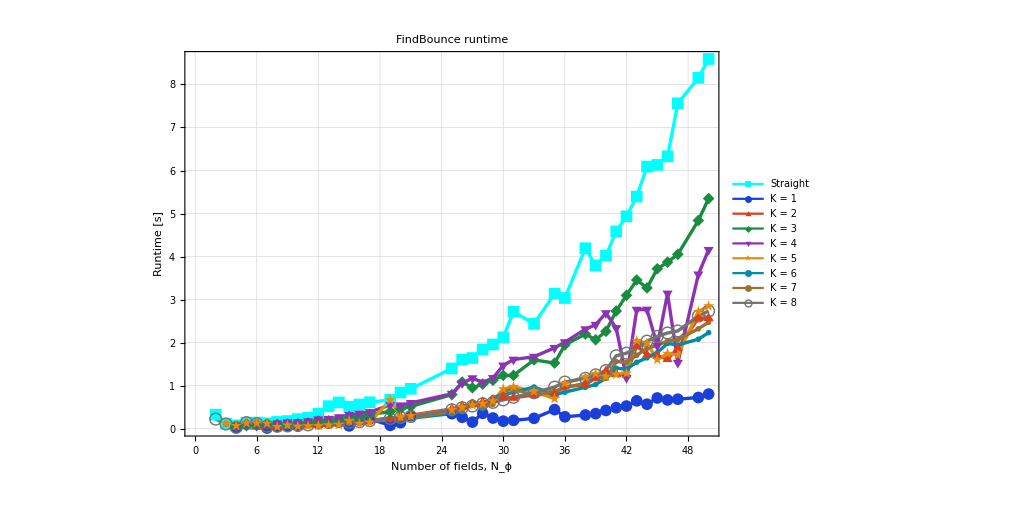

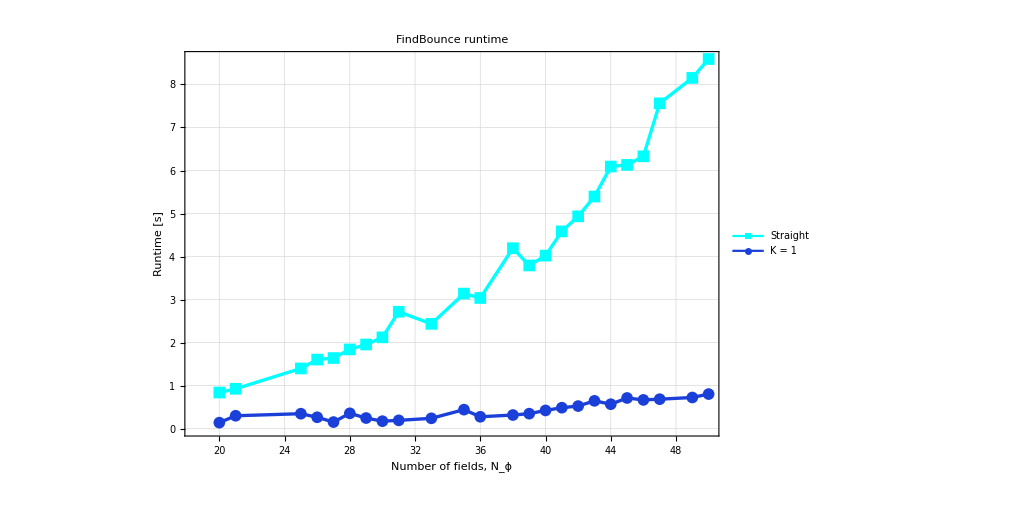

```mathematica
(* ============================================================*)(*FindBounce K-injection plotting script*)(* ============================================================*)

file="findbounce_csvK_scan_results.csv";
raw=Import[file,"CSV"];

head=raw[[1]];
rows=AssociationThread[head->#]&/@raw[[2;;]];

clean[x_]:=StringReplace[ToString[x],"\""->""];
num[x_]:=Quiet@Check[ToExpression[clean[x]],Missing["NA"]];

data=Association[#,"n"->num[#["nphi"]],"method2"->clean[#["method"]],"status2"->clean[#["status"]],"action"->num[#["ActionFindBounceD4"]],"time"->num[#["TimeSeconds"]]]&/@rows;

good=Select[data,#["status2"]=="ok"&&NumberQ[#["n"]]&&NumberQ[#["time"]]&];

(*------------------------------------------------------------*)
(*Helper function*)
(*------------------------------------------------------------*)

series[col_,m_,nmin_:-Infinity]:=SortBy[({#["n"],#[col]}&/@Select[good,#["method2"]==m&&NumberQ[#[col]]&&#["n"]>=nmin&]),First];

(*------------------------------------------------------------*)
(*Methods and paper-readable labels*)
(*------------------------------------------------------------*)

methodsAll={"straight","csvK1","csvK2","csvK3","csvK4","csvK5","csvK6","csvK7","csvK8"};

methodLabel=<|"straight"->"Straight","csvK1"->"K = 1","csvK2"->"K = 2","csvK3"->"K = 3","csvK4"->"K = 4","csvK5"->"K = 5","csvK6"->"K = 6","csvK7"->"K = 7","csvK8"->"K = 8"|>;

labelsAll=methodLabel/@methodsAll;

methodsK1={"straight","csvK1"};
labelsK1=methodLabel/@methodsK1;

(*------------------------------------------------------------*)
(*Plot style*)
(*------------------------------------------------------------*)

colors={RGBColor[0,1,1],RGBColor[0.10,0.25,0.85],RGBColor[0.85,0.25,0.10],RGBColor[0.10,0.55,0.25],RGBColor[0.55,0.20,0.70],RGBColor[0.90,0.55,0.05],RGBColor[0.00,0.55,0.65],RGBColor[0.60,0.45,0.20],RGBColor[0.45,0.45,0.45]};

markers={{"■",12},{"●",12},{"▲",12},{"◆",12},{"▼",12},{"★",12},{"◀",12},{"▶",12},{"○",12}};

lineStyles=Directive[#,AbsoluteThickness[2.4]]&/@colors;

commonOptions={Frame->True,Axes->False,ImageSize->760,AspectRatio->0.68,FrameStyle->Directive[Black,AbsoluteThickness[1.2]],FrameTicksStyle->Directive[Black,18],LabelStyle->Directive[Black,21],BaseStyle->{FontFamily->"Times",FontSize->18},GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.82],Dashed],PlotRange->All,PlotRangePadding->Scaled[0.045]};

legendAll=Placed[LineLegend[colors,labelsAll,LegendMarkerSize->16,LabelStyle->Directive[Black,16,FontFamily->"Times"],LegendLayout->{"Column",2}],Right];

legendK1=Placed[LineLegend[colors[[1;;2]],labelsK1,LegendMarkerSize->18,LabelStyle->Directive[Black,17,FontFamily->"Times"],LegendLayout->"Column"],Right];

(*------------------------------------------------------------*)
(*Appendix plot:full K-scan action*)
(*------------------------------------------------------------*)

pAction=ListLinePlot[series["action",#]&/@methodsAll,PlotStyle->lineStyles,PlotMarkers->markers,PlotLegends->legendAll,FrameLabel->{"Number of fields, \!\(\*SubscriptBox[\(N\), \(ϕ\)]\)","\!\(\*SubscriptBox[\(S\), \(4\)]\)"},PlotLabel->Style["FindBounce action",22,Bold,Black],Evaluate[Sequence@@commonOptions]];

(*------------------------------------------------------------*)
(*Appendix plot:full K-scan runtime*)
(*------------------------------------------------------------*)

pTime=ListLinePlot[series["time",#]&/@methodsAll,PlotStyle->lineStyles,PlotMarkers->markers,PlotLegends->legendAll,FrameLabel->{"Number of fields, \!\(\*SubscriptBox[\(N\), \(ϕ\)]\)","Runtime [s]"},PlotLabel->Style["FindBounce runtime",22,Bold,Black],Evaluate[Sequence@@commonOptions]];

(*------------------------------------------------------------*)
(*Main-text plot:K=1 only,high-dimensional rows only*)
(*This matches the main table N_phi=20,30,40,50.*)
(*------------------------------------------------------------*)

pTimeK1=ListLinePlot[series["time",#,20]&/@methodsK1,PlotStyle->lineStyles[[1;;2]],PlotMarkers->markers[[1;;2]],PlotLegends->legendK1,FrameLabel->{"Number of fields, \!\(\*SubscriptBox[\(N\), \(ϕ\)]\)","Runtime [s]"},PlotLabel->Style["FindBounce runtime",22,Bold,Black],Evaluate[Sequence@@commonOptions]];

pAction
pTime
pTimeK1

(*------------------------------------------------------------*)
(*Export*)
(*------------------------------------------------------------*)

plotDir=FileNameJoin[{NotebookDirectory[],"Plots"}];
If[!DirectoryQ[plotDir],CreateDirectory[plotDir]];

Export[FileNameJoin[{plotDir,"findbounce_csvK_action_vs_N.png"}],pAction,ImageResolution->300];

Export[FileNameJoin[{plotDir,"findbounce_csvK_time_vs_N.png"}],pTime,ImageResolution->300];

Export[FileNameJoin[{plotDir,"findbounce_k1_runtime_highdim.png"}],pTimeK1,ImageResolution->300];
```